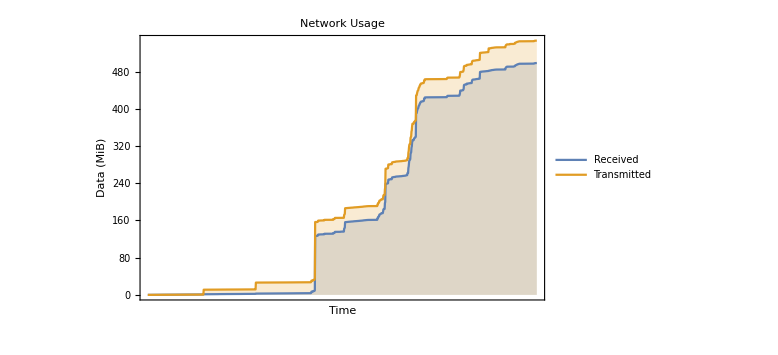

```mathematica
intItpr=Interpreter["Integer"];
range={DateObject[DateValue[{"Year","Month","Day"}]],Now};
range=ToString/@UnixTime/@range;
text=Import["http://bczhc.ml/server-network-log/get?time="<>range[[1]]<>".."<>range[[2]]<>"&bzip3=false","Text"];
handleLine[line_]:=intItpr@#&/@StringSplit[line];
data=handleLine@#&/@StringSplit[text,EndOfLine]//Parallelize;
data=({FromUnixTime@#[[1]],#[[2]],#[[3]]})&/@data;//Parallelize
firstRx=data[[1]][[2]];
firstTx=data[[1]][[3]];
data=({#[[1]],Quantity[#[[2]]-firstRx,"MiB"],Quantity[#[[3]]-firstTx,"MiB"]})&/@data//Parallelize;
rxData={#[[1]],#[[2]]/1048576}&/@data;
txData={#[[1]],#[[3]]/1048576}&/@data;
DateListPlot[{rxData,txData},ImageSize->Large,PlotLegends->{"Received","Transmitted"},FrameLabel->{"Time","Data (MiB)"},PlotLabel->"Network Usage",Filling->Bottom]
```